```mathematica
datadet1=Import["C:\\Users\\Lukas\\Dropbox\\1. Uni\\Bachelor\\BP-24 Bachelor Thesis\\20170720_Countrate_plastik\\Det1.csv", "FieldSeparators"->","];
datadet2=Import["C:\\Users\\Lukas\\Dropbox\\1. Uni\\Bachelor\\BP-24 Bachelor Thesis\\20170720_Countrate_plastik\\Det2.csv", "FieldSeparators"->","];
datcoinc=Import["C:\\Users\\Lukas\\Dropbox\\1. Uni\\Bachelor\\BP-24 Bachelor Thesis\\20170720_Countrate_plastik\\Coinc.csv", "FieldSeparators"->","];
```

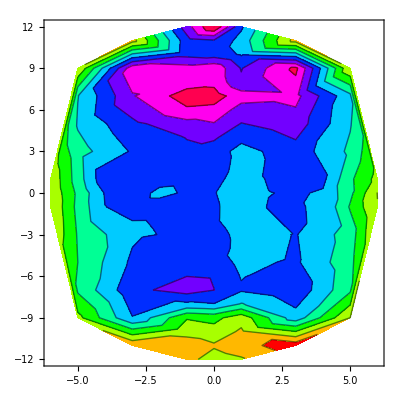

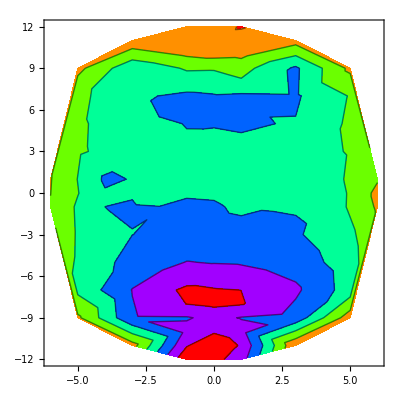

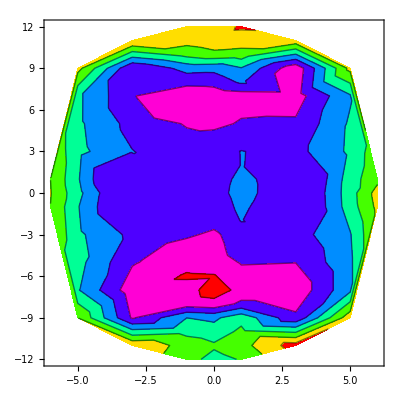

```mathematica
ListContourPlot[datadet1,ColorFunction->Hue,PlotRange->All]
ListContourPlot[datadet2,ColorFunction->Hue,PlotRange->All]
ListContourPlot[datcoinc, ColorFunction->Hue,PlotRange->All]
```

```mathematica
jet[u_?NumericQ]:=Blend[{{0,RGBColor[0,0,9/16]},{1/9,Blue},{23/63,Cyan},{13/21,Yellow},{47/63,Orange},{55/63,Red},{1,RGBColor[1/2,0,0]}},u]/;0≤u≤1
```

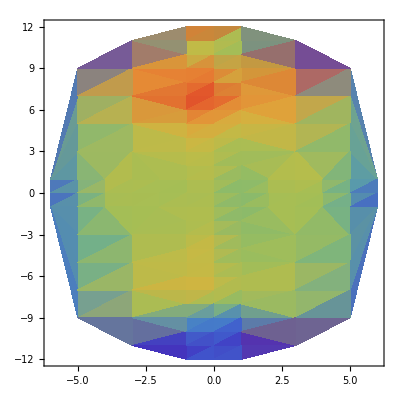

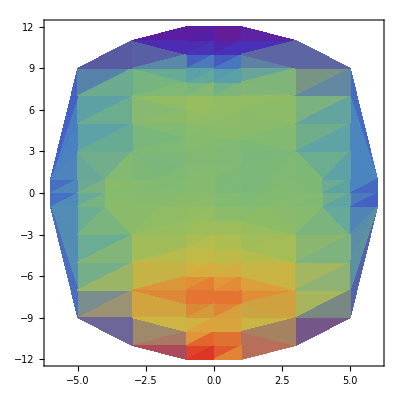

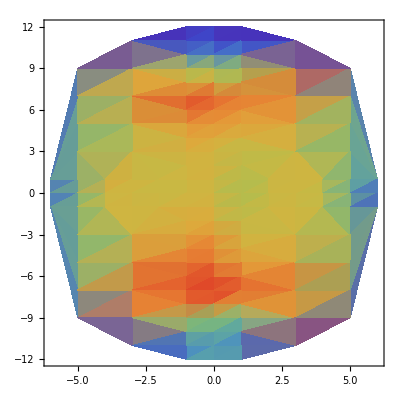

```mathematica
ListDensityPlot[datadet1,ColorFunction->"Rainbow",PlotRange->All]
ListDensityPlot[datadet2,ColorFunction->"Rainbow",PlotRange->All]
ListDensityPlot[datcoinc, ColorFunction->"Rainbow",PlotRange->All]
```

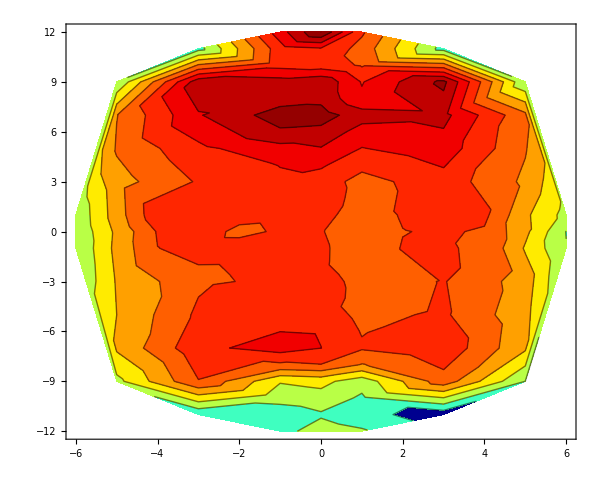

```mathematica
ListContourPlot[data,PlotLegends->Automatic,ColorFunction->(jet[(#)^.4]&),PlotRange->All,AspectRatio->24/30,ImageSize->600]
```